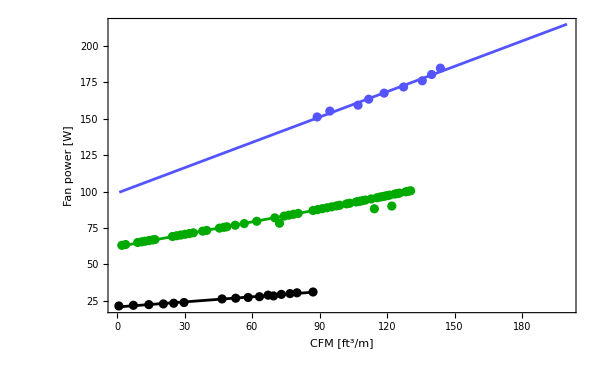

```mathematica
(*Fans*)
nfans=4;
QCFM=nfans{0.21,1.82,3.54,5.15,6.30,7.45,11.67,13.19,14.57,15.83,17.39,16.79,18.26,19.22,20.00,21.78};
Ptot=nfans{5.35698687,5.472198511,5.588634921,5.7062961,5.82518205,5.945292769,6.564217911,6.691677249,6.820361356,6.950270233,7.08140388,7.213762297,7.347345483,7.482153439,7.618186165,7.755443661};
QCFMP=Table[{QCFM[[i]],Ptot[[i]]},{i,1,Length[QCFM]}];
QCFM2=nfans{22.24,23.65,26.78,27.97,29.68,31.84,33.92,34.96,35.93};
Ptot2=nfans{37.82,38.82375,39.84,40.86875,41.91,42.96375,44.03,45.10875,46.2};
QCFMP2=Table[{QCFM2[[i]],Ptot2[[i]]},{i,1,Length[QCFM2]}];
SetDirectory[NotebookDirectory[]];
QCFM3=nfans Flatten[Import["text.dat"]];
Ptot3=nfans Flatten[Import["text2.dat"]];
QCFMP3=Table[{QCFM3[[i]],Ptot3[[i]]},{i,1,Length[QCFM3]}];
{a1,b1}={a,b}/.FindFit[QCFMP,a+b x,{a,b},x];
{a2,b2}={a,b}/.FindFit[QCFMP2,a+b x,{a,b},x];
{a3,b3}={a,b}/.FindFit[QCFMP3,a+b x,{a,b},x];
Show[Plot[a1+b1 x,{x,0,QCFM[[-1]]},PlotRange->{{0,200.},All},PlotRange->All,Frame->True,PlotStyle->Black,ImageSize->600,FrameLabel->{"CFM [ft^3/m]","Fan power [W]"},FrameStyle->Directive[Black,18]],Plot[a2+b2 x,{x,1,200},PlotRange->All,PlotStyle->Lighter[Blue]],Plot[a3+b3 x,{x,QCFM3[[1]],Max[QCFM3]},PlotRange->All,PlotStyle->Darker[Green]],
ListPlot[{QCFMP,QCFMP2,QCFMP3},PlotStyle->{Black,Lighter[Blue],Darker[Green]}]]
fCFMtoPower[CFM_]:=If[CFM<QCFMP[[-1,1]],a1+b1 CFM,If[CFM<Max[QCFMP3[[All,1]]] ,a3+b3 CFM,a2+b2 CFM]]
(*fCFMtoPower[CFM_]:=a2+b2 CFM*)
```

```mathematica
{0.1,0.2,0.5,1,2,5,10}*3.54 10^6
```

{354000.,708000.,1.77×10^6,3.54×10^6,7.08×10^6,1.77×10^7,3.54×10^7}

```mathematica
{0.1,0.2,0.5,1,2,5,10}*6.25 10^7
```

{6.25×10^6,1.25×10^7,3.125×10^7,6.25×10^7,1.25×10^8,3.125×10^8,6.25×10^8}

```mathematica
(*{{5,},{10,},{20,},{40,},{60,},{80,},{100,},{120,},{140,},{160,},{180,},{200,}}*)
```

```mathematica
(*16 cores, 10 fins, no hotspot, air*)
T1nh={{5,300.5},{10,202.4},{20,154},{40,121.9},{60,104.6},{80,94.6},{100,88.8},{120,85},{140,82.3},{160,80.4},{180,78.9},{200,77.6}};
(*16 cores, 10 fins, hotspot, air*)
T1h={{5,381.2},{10,268.7},{20,212.4},{40,175.1},{60,154.9},{80,143.3},{100,136.5},{120,132},{140,129},{160,126.7},{180,124.9},{200,123.5}};
```

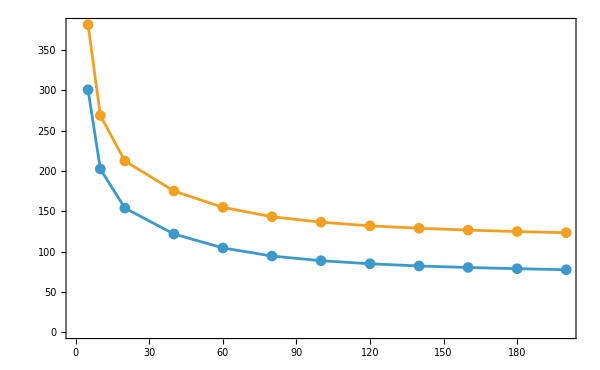

```mathematica
ListPlot[{T1nh,T1h},Joined->True,Mesh->All,Frame->True,ImageSize->600]
```

```mathematica
(*Power in one hotspot*)
6.25 10^7(200 10^-6)^2
(*Power in all hotspots*)
16%
(*Total laser power required*)
%/0.2 0.5
```

2.5

40.

100.

```mathematica
16%
```

1600.

```mathematica
F[NOHS_,HS_,TOTLasPower_,LasPower_]:=Table[{NOHS[[i,1]],HS[[i,2]]+LasPower/TOTLasPower(NOHS[[i,2]]-HS[[i,2]])},{i,1,Length[NOHS]}]
```

```mathematica
Manipulate[Show[ListPlot[{T1nh,T1h,F[T1nh,T1h,100.,LasPower]},Frame->True,FrameLabel->{"CFM [ft^3/m]","T_hs(C)"},Joined->True,Mesh->All,ImageSize->600],Plot[Tfinal,{x,0,200},PlotStyle->{Black,Dashed}]],{LasPower,0,100},{{Tfinal,120},50,300}]
```

```mathematica
fCFM[CFM_,NOHS_,HS_,TOTLasPower_,LasPower_]:=Interpolation[F[NOHS,HS,TOTLasPower,LasPower],InterpolationOrder->1][CFM]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

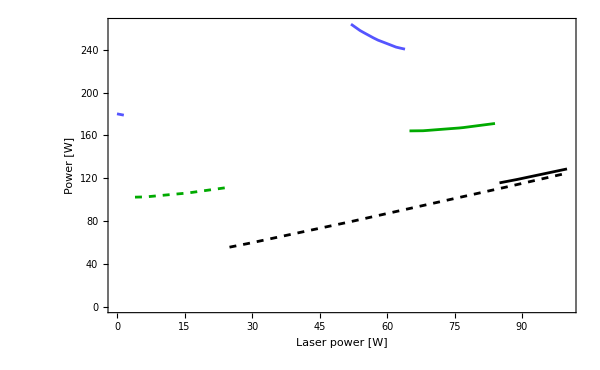

```mathematica
t1=Table[{LasPower,LasPower+fCFMtoPower[CFM/.FindRoot[fCFM[CFM,T1nh,T1h,100.,LasPower]==100,{CFM,120}]]},{LasPower,52,64,1}];
t2=Table[{LasPower,LasPower+fCFMtoPower[CFM/.FindRoot[fCFM[CFM,T1nh,T1h,100.,LasPower]==100,{CFM,120}]]},{LasPower,65,84,1}];
t3=Table[{LasPower,LasPower+fCFMtoPower[CFM/.FindRoot[fCFM[CFM,T1nh,T1h,100.,LasPower]==100,{CFM,120}]]},{LasPower,85,100,1}];
t4=Table[{LasPower,LasPower+fCFMtoPower[CFM/.FindRoot[fCFM[CFM,T1nh,T1h,100.,LasPower]==129,{CFM,50}]]},{LasPower,0,3,1}];
t5=Table[{LasPower,LasPower+fCFMtoPower[CFM/.FindRoot[fCFM[CFM,T1nh,T1h,100.,LasPower]==129,{CFM,50}]]},{LasPower,4,24,1}];
t6=Table[{LasPower,LasPower+fCFMtoPower[CFM/.FindRoot[fCFM[CFM,T1nh,T1h,100.,LasPower]==129,{CFM,50}]]},{LasPower,25,100,1}];
ListPlot[{t1,t2,t3,t4,t5,t6},Frame->True,PlotRange->{{0,100},All},ImageSize->600,PlotStyle->{{Lighter[Blue]},{Darker[Green]},{Black},{Lighter[Blue],Dashed},{Darker[Green],Dashed},{Black,Dashed}},FrameLabel->{"Laser power [W]","Power [W]"},FrameStyle->Directive[Black,26],Joined->True]
```

```mathematica
(*16 cores, 20 fins, no hotspot, air*)
T2nh={{5,339.1},{10,208.4},{20,136.7},{40,103.5},{60,92.7},{80,85.8},{100,81.8},{120,79.2},{140,77.5},{160,76.1},{180,75},{200,74.2}};
(*16 cores, 20 fins, hotspot, air*)
T2h={{5,426.2},{10,277.6},{20,194.6},{40,155.8},{60,143.2},{80,135.2},{100,130.5},{120,127.5},{140,125.4},{160,123.9},{180,122.7},{200,121.7}};
```

```mathematica
Manipulate[Show[ListPlot[{T2nh,T2h,F[T2nh,T2h,100.,LasPower]},Frame->True,FrameLabel->{"CFM [ft^3/m]","T_hs(C)"},Joined->True,Mesh->All,ImageSize->600],Plot[Tfinal,{x,0,200},PlotStyle->{Black,Dashed}]],{LasPower,0,100},{{Tfinal,120},50,300}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

InterpolatingFunction::dmval: Input value {3.27264} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {200.87} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {221.429} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {214.448} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {200.304} lies outside the range of data in the interpolating function. Extrapolation will be used.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

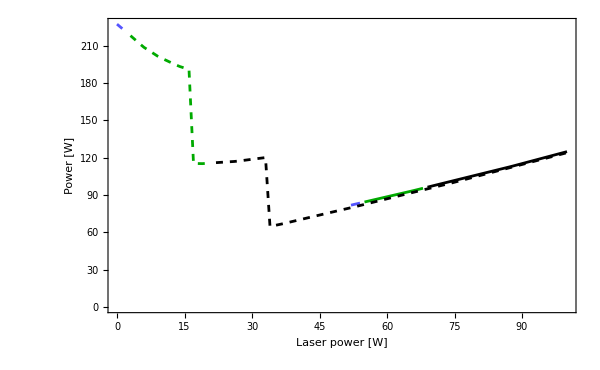

```mathematica
t1b=Table[{LasPower,LasPower+fCFMtoPower[CFM/.FindRoot[fCFM[CFM,T2nh,T2h,100.,LasPower]==110,{CFM,50}]]},{LasPower,52,54,1}];
t2b=Table[{LasPower,LasPower+fCFMtoPower[CFM/.FindRoot[fCFM[CFM,T2nh,T2h,100.,LasPower]==110,{CFM,50}]]},{LasPower,55,68,1}];
t3b=Table[{LasPower,LasPower+fCFMtoPower[CFM/.FindRoot[fCFM[CFM,T2nh,T2h,100.,LasPower]==110,{CFM,100}]]},{LasPower,69,100,1}];
t4b=Table[{LasPower,LasPower+fCFMtoPower[CFM/.FindRoot[fCFM[CFM,T2nh,T1h,100.,LasPower]==122,{CFM,50}]]},{LasPower,0,2,1}];
t5b=Table[{LasPower,LasPower+fCFMtoPower[CFM/.FindRoot[fCFM[CFM,T2nh,T1h,100.,LasPower]==122,{CFM,50}]]},{LasPower,3,21,1}];
t6b=Table[{LasPower,LasPower+fCFMtoPower[CFM/.FindRoot[fCFM[CFM,T2nh,T1h,100.,LasPower]==122,{CFM,50}]]},{LasPower,22,100,1}];
ListPlot[{t1b,t2b,t3b,t4b,t5b,t6b},Frame->True,PlotRange->{{0,100},All},ImageSize->600,PlotStyle->{{Lighter[Blue]},{Darker[Green]},{Black},{Lighter[Blue],Dashed},{Darker[Green],Dashed},{Black,Dashed}},FrameLabel->{"Laser power [W]","Power [W]"},FrameStyle->Directive[Black,26],Joined->True]
```

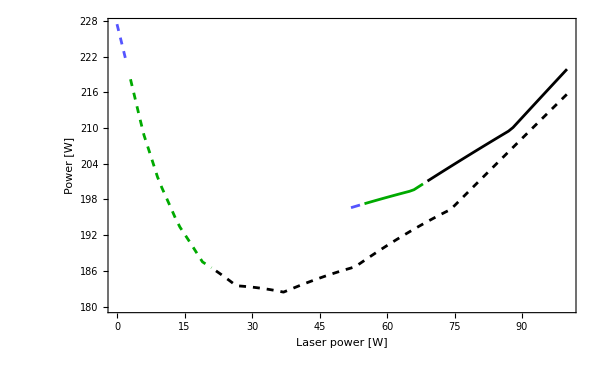

```mathematica
asdasd
```

```mathematica
Manipulate[t1b=Table[{LasPower,LasPower+fCFMtoPower[CFM/.FindRoot[fCFM[CFM,T2nh,T2h,100.,LasPower]==Tcolder,{CFM,50}]]},{LasPower,0,13,1}];
t2b=Table[{LasPower,LasPower+fCFMtoPower[CFM/.FindRoot[fCFM[CFM,T2nh,T2h,100.,LasPower]==Tcolder,{CFM,50}]]},{LasPower,14,27,1}];
t3b=Table[{LasPower,LasPower+fCFMtoPower[CFM/.FindRoot[fCFM[CFM,T2nh,T2h,100.,LasPower]==Tcolder,{CFM,50}]]},{LasPower,28,100,1}];
t4b=Table[{LasPower,LasPower+fCFMtoPower[CFM/.FindRoot[fCFM[CFM,T2nh,T2h,100.,LasPower]==Thotter,{CFM,50}]]},{LasPower,0,2,1}];
t5b=Table[{LasPower,LasPower+fCFMtoPower[CFM/.FindRoot[fCFM[CFM,T2nh,T2h,100.,LasPower]==Thotter,{CFM,50}]]},{LasPower,3,21,1}];
t6b=Table[{LasPower,LasPower+fCFMtoPower[CFM/.FindRoot[fCFM[CFM,T2nh,T2h,100.,LasPower]==Thotter,{CFM,50}]]},{LasPower,22,100,1}];
ListPlot[{t1b,t2b,t3b,t4b,t5b,t6b},Frame->True,PlotRange->{{0,100},All},ImageSize->600,PlotStyle->{{Lighter[Blue]},{Darker[Green]},{Black},{Lighter[Blue],Dashed},{Darker[Green],Dashed},{Black,Dashed}},FrameLabel->{"Laser power [W]","Power [W]"},FrameStyle->Directive[Black,26],Joined->True],{{Thotter,129},120,140},{{Tcolder,120},78,Thotter}]
```

InterpolatingFunction::dmval: Input value {212.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {234.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {205.657} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {212.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {234.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {205.657} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {212.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {234.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {205.657} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {4.50872} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {4.50872} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {4.22222} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {220.907} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {386.72} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {217.817} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {220.907} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {386.72} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {217.817} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {640.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {876.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {633.943} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {676.96} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {931.44} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {670.927} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

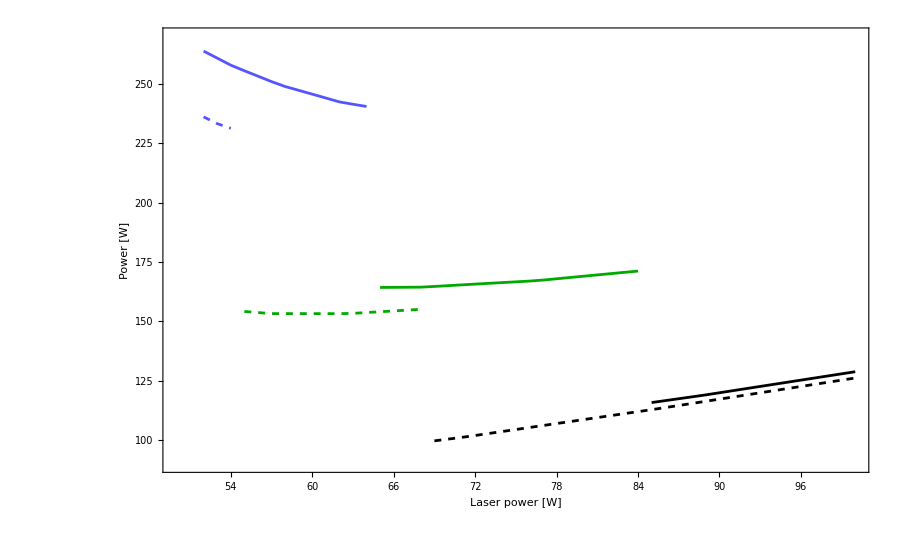

```mathematica
ListPlot[{t1,t2,t3,t1b,t2b,t3b},Frame->True,PlotRange->{{50,100},{90,270}},ImageSize->600,PlotStyle->{{Lighter[Blue]},{Darker[Green]},{Black},{Lighter[Blue],Dashed},{Darker[Green],Dashed},{Black,Dashed}},FrameLabel->{"Laser power [W]","Power [W]"},FrameStyle->Directive[Black,26],Joined->True]
```

```mathematica
85, 115.8, 85+35.8
95, 124.4,95+34.4
```

```mathematica
Manipulate[Show[ListPlot[{T1nh,T1h,T2nh,T2h,F[T1nh,T1h,100.,LasPower],F[T2nh,T2h,100.,LasPower]},Frame->True,FrameLabel->{"CFM [ft^3/m]","T_hs(C)"},Joined->True,Mesh->All,ImageSize->600,PlotStyle->{{Black},{Red},{Black,Dashed},{Red,Dashed},{Blue},{Blue,Dashed}}],Plot[Tfinal,{x,0,200},PlotStyle->{Gray,Dashed}]],{LasPower,0,100},{{Tfinal,100},50,300}]
```

```mathematica
(*16 cores, 20 fins, no hotspot, water*)
T3nh={{5,54.91},{10,52.89},{20,51.26},{40,50.66},{60,50.5},{80,50.45},{100,50.4},{120,50.4},{140,50.4},{160,50.4},{180,50.4},{200,50.4}};
(*16 cores, 20 fins, hotspot, water*)
T3h={{5,100.1},{10,97.88},{20,96.11},{40,95.47},{60,95.3},{80,95.26},{100,95.24},{120,95.2},{140,95.2},{160,95.2},{180,95.2},{200,95.1}};
```

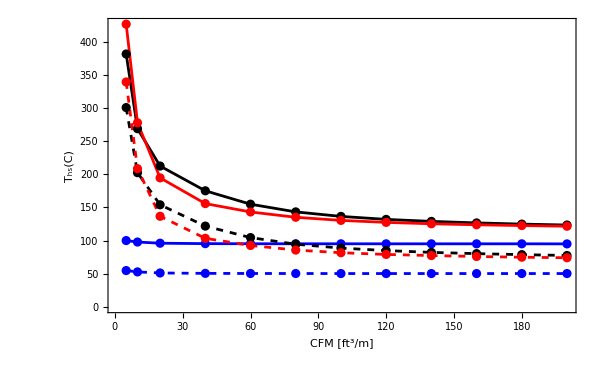

```mathematica
ListPlot[{T1h,T2h,T3h,T1nh,T2nh,T3nh},Frame->True,FrameLabel->{"CFM [ft^3/m]","T_hs(C)"},Joined->True,Mesh->All,ImageSize->600,PlotStyle->{{Black},{Red},{Blue},{Black,Dashed},{Red,Dashed},{Blue,Dashed}},PlotRange->All]
```

```mathematica
(*16 cores, 20 fins, hotspot, changes in section and length*)
reference={{5,425.7},{10,276.9},{20,193.8},{40,155},{60,142.4},{80,134.4},{100,129.7},{120,126.7},{140,124.6},{160,123.1},{180,121.8},{200,120.9}};
doublesection={{5,409.2},{10,266.2},{20,190.8},{40,154.6},{60,143.2},{80,136.9},{100,132.7},{120,129.6},{140,127.4},{160,125.8},{180,124.6},{200,123.6}};
doublelength={{5,447.2},{10,294.4},{20,203.2},{40,159.2},{60,145.1},{80,137.7},{100,133.3},{120,130.4},{140,128.3},{160,126.7},{180,125.4},{200,124.4}};
doubleboth={{5,422.6},{10,274.1},{20,196},{40,156},{60,143.1},{80,136.3},{100,132.3},{120,129.6},{140,127.7},{160,126.3},{180,125.2},{200,124.2}};
```

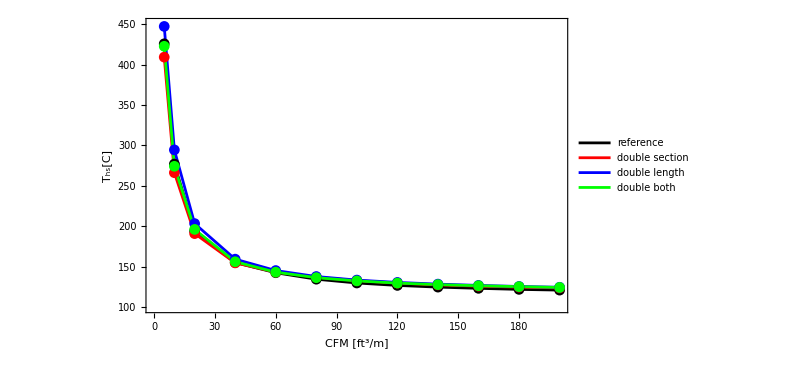

```mathematica
ListPlot[{reference,doublesection,doublelength,doubleboth},Frame->True,FrameLabel->{"CFM [ft^3/m]","T_hs[C]"},Joined->True,Mesh->All,ImageSize->600,PlotStyle->{{Black},{Red},{Blue},{Green}},PlotRange->{100,450},PlotLegends->Placed[{"reference","double section","double length","double both"},Scaled[{0.8,0.8}]]]
```

```mathematica
"
```

```mathematica
(*16 cores, 20 fins, uniform sink, air*)
uniformsink={{5,325.8},{10,201.5},{20,133.8},{40,102.4},{60,92.24},{80,85.83},{100,82.05},{120,79.64},{140,77.97},{160,76.71},{180,75.73},{200,74.94}};
(*16 cores, 20 fins, localized sink, air*)
localizedsink={{5,339.7},{10,209.9},{20,138.8},{40,105.8},{60,95.07},{80,88.32},{100,84.35},{120,81.8},{140,80},{160,78.72},{180,77.69},{200,76.86}};
(*16 cores, 20 fins, no sink, air*)
hotspot={{5,425.7},{10,276.9},{20,193.8},{40,155},{60,142.4},{80,134.4},{100,129.7},{120,126.7},{140,124.6},{160,123.1},{180,121.8},{200,120.9}};
(*16 cores, 20 fins, no sink, no hotspot, air*)
nohotspot={{5,338.6},{10,207.6},{20,135.9},{40,102.6},{60,91.72},{80,84.9},{100,80.89},{120,78.32},{140,76.55},{160,75.21},{180,74.17},{200,73.33}};
(*16 cores, 20 fins, no sink, no hotspot, air, mesh 6*)
nohotspotmesh6={{5,344.6},{10,206.4},{20,135.4},{40,102.3},{60,91.36},{80,85.1},{100,80.76},{120,77.93},{140,75.95},{160,74.49},{180,73.37},{200,72.46}};
```

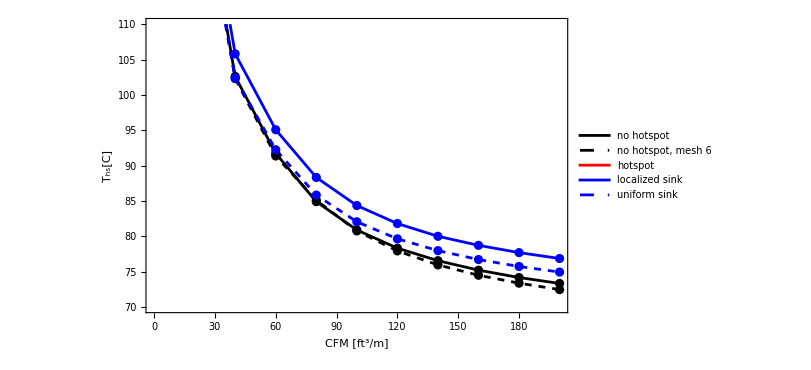

```mathematica
ListPlot[{nohotspot,nohotspotmesh6,hotspot,localizedsink,uniformsink},Frame->True,FrameLabel->{"CFM [ft^3/m]","T_hs[C]"},Joined->True,Mesh->All,ImageSize->600,PlotStyle->{{Black},{Black,Dashed},{Red},{Blue},{Blue,Dashed}},PlotRange->{70,110},PlotLegends->{"no hotspot","no hotspot, mesh 6","hotspot","localized sink","uniform sink"}]
```

```mathematica
floc[CFM_]:=Interpolation[localizedsink,InterpolationOrder->1][CFM]
funi[CFM_]:=Interpolation[uniformsink,InterpolationOrder->1][CFM]
```

```mathematica
fCFMtoPower[CFM/.FindRoot[floc[CFM]==80,{CFM,120}]]
fCFMtoPower[CFM/.FindRoot[funi[CFM]==80,{CFM,120}]]
```

180.196

95.4768

```mathematica
CFM/.FindRoot[floc[CFM]==97,{CFM,60}]
```

56.4026

```mathematica
6.25 10^12(200 10^-6)^2 10 10^-6 16/0.2 0.5
2.8 10^9((20 10^-3)^2-16(200 10^-6)^2)10 10^-6/0.2 0.5
```

100.

27.9552

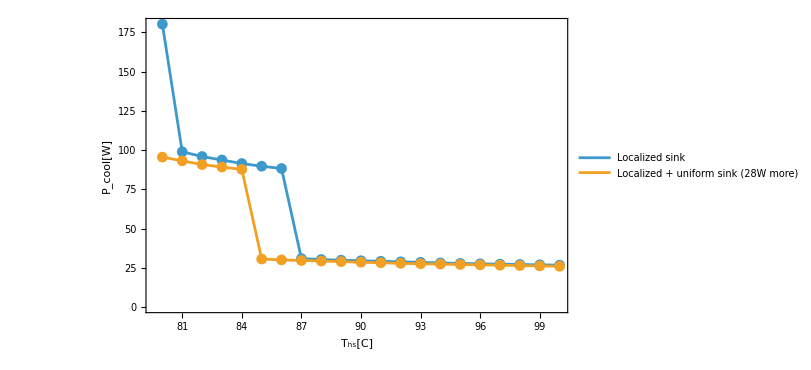

```mathematica
Tloc=Table[{TT,fCFMtoPower[CFM/.FindRoot[floc[CFM]==TT,{CFM,100}]]},{TT,80,100}];
Tuni=Table[{TT,fCFMtoPower[CFM/.FindRoot[funi[CFM]==TT,{CFM,100}]]},{TT,80,100}];
ListPlot[{Tloc,Tuni},PlotRange->All,Joined->True,Mesh->All,Frame->True,ImageSize->600,FrameLabel->{"T_hs[C]","P_cool[W]"},PlotLegends->Placed[{"Localized sink","Localized + uniform sink (28W more)"},Scaled[{0.7,0.8}]]]
```

```mathematica
fCFMtoPower[131]
fCFMtoPower[130]
fCFMtoPower[87]
fCFMtoPower[86]
```

174.972

99.1885

30.8679

30.7513